```mathematica
f[x_]:=(4275)*((Sin[Pi*0.1*Sin[(x-4)/50]/(0.000546)]*(0.000546/(Pi*0.1*Sin[(x-4)/50])))^2)*(Cos[Pi*0.406*Sin[(x-4)/50]/0.000546]^2);
Table[f[x],{x,0,8,0.05}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

{0.0941799,0.597348,1.16417,0.107981,0.00321577,0.532446,2.31007,1.08812,0.000409018,0.000669384,0.832959,1.02948,0.016893,0.934442,0.176741,0.1088,0.0619859,2.25608,2.51618,0.219588,0.000826632,1.01017,3.00349,0.675327,0.277863,0.165575,0.458579,0.331025,0.972302,3.45551,0.843852,0.00270986,0.607079,5.02749,3.87951,0.0719655,0.0752056,1.04107,2.94948,0.0345451,2.66131,1.56061,0.0775017,0.00168159,4.96573,9.66628,1.96916,0.00243065,1.43715,9.49045,4.77106,0.383121,1.77086,0.505347,2.2706,1.44217,15.6523,8.41745,0.0412433,0.782871,20.7276,30.2225,3.26695,0.990934,2.14066,22.9341,4.93257,16.5014,28.6315,0.160629,1.32295,41.0257,194.221,101.072,0.487741,14.1378,444.661,784.623,4.36435,1834.8,Indeterminate,1834.8,4.36435,784.623,444.661,14.1378,0.487741,101.072,194.221,41.0257,1.32295,0.160629,28.6315,16.5014,4.93257,22.9341,2.14066,0.990934,3.26695,30.2225,20.7276,0.782871,0.0412433,8.41745,15.6523,1.44217,2.2706,0.505347,1.77086,0.383121,4.77106,9.49045,1.43715,0.00243065,1.96916,9.66628,4.96573,0.00168159,0.0775017,1.56061,2.66131,0.0345451,2.94948,1.04107,0.0752056,0.0719655,3.87951,5.02749,0.607079,0.00270986,0.843852,3.45551,0.972302,0.331025,0.458579,0.165575,0.277863,0.675327,3.00349,1.01017,0.000826632,0.219588,2.51618,2.25608,0.0619859,0.1088,0.176741,0.934442,0.016893,1.02948,0.832959,0.000669384,0.000409018,1.08812,2.31007,0.532446,0.00321577,0.107981,1.16417,0.597348,0.0941799}

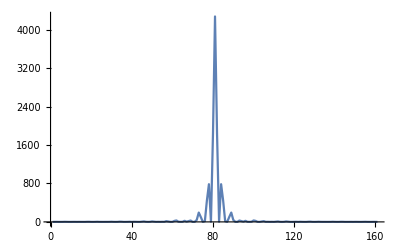

```mathematica
values={0.09417990286565009,0.597348094962341,1.1641727806539288,0.1079811409419769,0.00321577427267143,0.5324463185037749,2.3100724573600284,1.0881237041188425,0.0004090184038527017,0.0006693841806144757,0.8329594266445429,1.0294781010978638,0.01689300316170057,0.9344419560425634,0.17674108069258235,0.10880049400106581,0.06198587846664144,2.25607648880668,2.516178364285729,0.21958778513341187,0.0008266319149354533,1.0101739729366621,3.00349135039014,0.6753273138070014,0.2778632070255437,0.16557520590632965,0.45857886051772234,0.33102535031169406,0.9723023479074276,3.4555138583794807,0.8438520166529763,0.0027098590856871,0.6070791465045274,5.027485506338878,3.879505287414121,0.07196547588924466,0.07520557622750167,1.0410671003768295,2.9494759319861856,0.034545104814338215,2.6613084148899313,1.5606058366605227,0.07750173972148777,0.00168159369482055,4.9657259808173055,9.666278541920255,1.9691622721402375,0.0024306466474230165,1.4371488202981777,9.490445377958725,4.771055246584054,0.3831211293817229,1.770855561762932,0.5053473684138649,2.2705984386154405,1.4421660358771426,15.65228879499616,8.41745051878033,0.04124326478826851,0.7828707766897182,20.7275604797942,30.222491734044198,3.266950500195198,0.9909337932203318,2.1406572367263577,22.93412831338926,4.9325696717106915,16.501408385033493,28.631472140675594,0.16062923426675124,1.3229520204991165,41.02572410387348,194.22083392488858,101.07221835723062,0.4877412362990135,14.137837866305485,444.6605715093542,784.622886356077,4.364348054807649,1834.8040870511554,4275,1834.8040870511554,4.3643480547987625,784.6228863560418,444.6605715093499,14.137837866305485,0.4877412362990135,101.07221835722594,194.22083392488983,41.02572410387568,1.3229520204991165,0.16062923426675124,28.63147214067684,16.501408385035194,4.932569671709949,22.93412831338926,2.1406572367262426,0.9909337932205449,3.2669505001949783,30.222491734043828,20.7275604797942,0.7828707766898391,0.04124326478827235,8.417450518780317,15.652288794996533,1.4421660358771426,2.270598438615054,0.5053473684137827,1.7708555617630253,0.38312112938183834,4.771055246584054,9.490445377958471,1.437148820298205,0.0024306466474244303,1.9691622721401196,9.666278541920255,4.965725980817778,0.0016815936948251704,0.07750173972148129,1.5606058366605933,2.6613084148899313,0.03454510481430896,2.9494759319859476,1.041067100376786,0.07520557622750167,0.07196547588924466,3.8795052874140574,5.027485506338916,0.6070791465045491,0.0027098590856871,0.8438520166529763,3.4555138583796685,0.9723023479075896,0.3310253503116639,0.45857886051772234,0.16557520590632965,0.2778632070256316,0.6753273138069201,3.0034913503901226,1.0101739729366621,0.0008266319149354533,0.2195877851334015,2.5161783642857145,2.2560764888067575,0.06198587846664144,0.10880049400106581,0.1767410806925922,0.9344419560425634,0.01689300316170057,1.0294781010978638,0.8329594266445429,0.0006693841806132997,0.0004090184038527017,1.088123704118745,2.3100724573600284,0.5324463185037749,0.0032157742726684944,0.10798114094197332,1.1641727806539672,0.597348094962341,0.09417990286565009};
ListPlot[values,Joined->True,PlotRange->All]
```

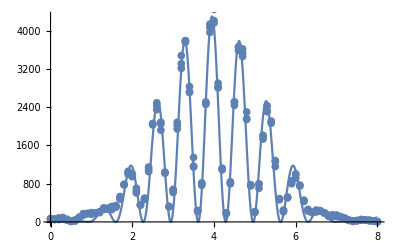

```mathematica
data = Import["desktop/445mmAll.csv"];
I0 = 4300;
a = 0.08;
d = 0.406;
lambda = 0.000546;
x0 = 3.95;
fit = Plot[I0*((Sin[Pi*a*Sin[(x-x0)/500]/(lambda)]*(lambda/(Pi*a*Sin[(x-x0)/500])))^2)*(Cos[Pi*d*Sin[(x-x0)/500]/lambda]^2),{x,0,8}];
dataPlot = ListPlot[data];
Show[fit,dataPlot]
```